## Compound Interest

```mathematica
rate=0.0351;
n=1;
t=30;
Accrual30[Principal_]:=Principal(1+rate/n)^(n*t)
Qmax=500000;
Qmin=200000;
Npt=30;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
AccrualTable30=Table[{Q[i],Accrual30[Q[i]]},{i,0,Npt}];
```

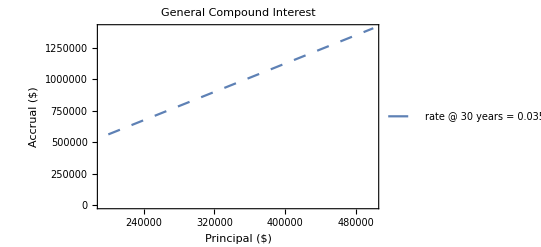

```mathematica
PlotAccrual30=ListPlot[%, Joined-> True,PlotStyle->{Dashing[Medium]},PlotLegends->{"rate @ 30 years = 0.0351"},Frame->True,FrameLabel->{"Principal ($)","Accrual ($)"},PlotLabel->HoldForm["General Compound Interest"],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

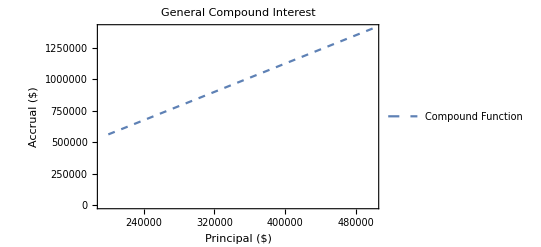

```mathematica
PlotAccrual30NT=ListPlot[%%, Joined-> True,PlotStyle->{Dashing[Small]},PlotLegends->{"Compound Function"},Frame->True,FrameLabel->{"Principal ($)","Accrual ($)"},PlotLabel->HoldForm["General Compound Interest"],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
rate=0.0295;
n=1;
t=15;
Accrual15[Principal_]:=Principal(1+rate/n)^(n*t)
Qmax=500000;
Qmin=200000;
Npt=30;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
AccrualTable15=Table[{Q[i],Accrual15[Q[i]]},{i,0,Npt}];
```

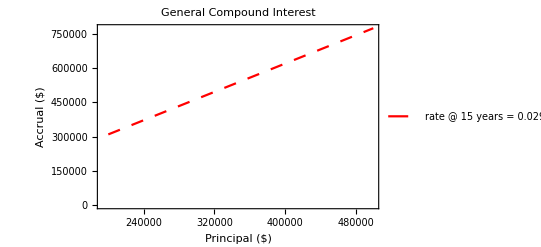

```mathematica
PlotAccrual15=ListPlot[%, Joined-> True,PlotStyle->{Dashing[Medium],Red},PlotLegends->{"rate @ 15 years = 0.0295"},Frame->True,FrameLabel->{"Principal ($)","Accrual ($)"},PlotLabel->HoldForm["General Compound Interest"],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

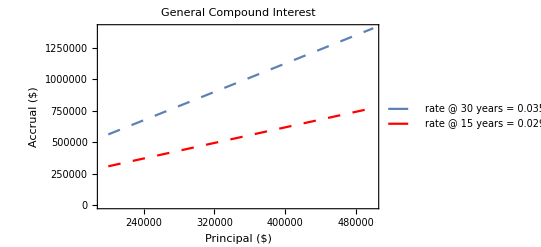

```mathematica
Show[PlotAccrual30,PlotAccrual15]
```

```mathematica
AccrualTable30
AccrualTable15
```

(200000 | 562988.
210000 | 591138.
220000 | 619287.
230000 | 647436.
240000 | 675586.
250000 | 703735.
260000 | 731885.
270000 | 760034.
280000 | 788183.
290000 | 816333.
300000 | 844482.
310000 | 872632.
320000 | 900781.
330000 | 928930.
340000 | 957080.
350000 | 985229.
360000 | 1.01338×10^6
370000 | 1.04153×10^6
380000 | 1.06968×10^6
390000 | 1.09783×10^6
400000 | 1.12598×10^6
410000 | 1.15413×10^6
420000 | 1.18228×10^6
430000 | 1.21042×10^6
440000 | 1.23857×10^6
450000 | 1.26672×10^6
460000 | 1.29487×10^6
470000 | 1.32302×10^6
480000 | 1.35117×10^6
490000 | 1.37932×10^6
500000 | 1.40747×10^6)

(200000 | 309332.
210000 | 324799.
220000 | 340266.
230000 | 355732.
240000 | 371199.
250000 | 386665.
260000 | 402132.
270000 | 417599.
280000 | 433065.
290000 | 448532.
300000 | 463998.
310000 | 479465.
320000 | 494932.
330000 | 510398.
340000 | 525865.
350000 | 541332.
360000 | 556798.
370000 | 572265.
380000 | 587731.
390000 | 603198.
400000 | 618665.
410000 | 634131.
420000 | 649598.
430000 | 665064.
440000 | 680531.
450000 | 695998.
460000 | 711464.
470000 | 726931.
480000 | 742398.
490000 | 757864.
500000 | 773331.)

## Payments Per Month (Compounded)

```mathematica
rate=0.0351;
n=1;
t=30;
Accrual30perMonth[Principal_]:=Principal(1+rate/n)^(n*t)/(360)
Qmax=500000;
Qmin=200000;
Npt=30;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
AccrualTable30perMonth=Table[{Q[i],Accrual30perMonth[Q[i]]},{i,0,Npt}];
```

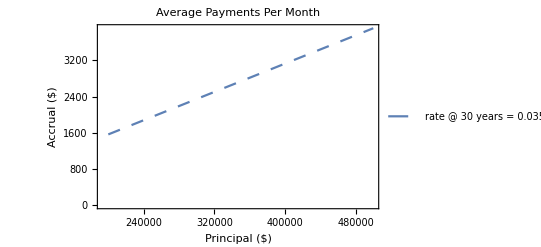

```mathematica
PlotAccrual30perMonth=ListPlot[%, Joined-> True,PlotStyle->{Dashing[Medium]},PlotLegends->{"rate @ 30 years = 0.0351"},Frame->True,FrameLabel->{"Principal ($)","Accrual ($)"},PlotLabel->HoldForm["Average Payments Per Month"],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
rate=0.0295;
n=1;
t=15;
Accrual15perMonth[Principal_]:=Principal(1+rate/n)^(n*t)/(180)
Qmax=500000;
Qmin=200000;
Npt=30;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
AccrualTable15perMonth=Table[{Q[i],Accrual15perMonth[Q[i]]},{i,0,Npt}];
```

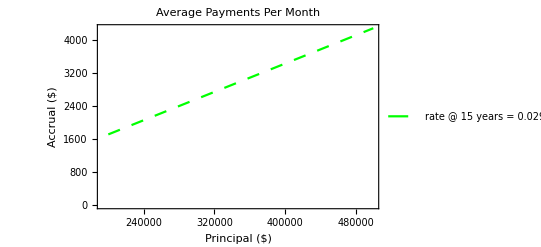

```mathematica
PlotAccrual15perMonth=ListPlot[%, Joined-> True,PlotStyle->{Dashing[Medium],Green},PlotLegends->{"rate @ 15 years = 0.0295"},Frame->True,FrameLabel->{"Principal ($)","Accrual ($)"},PlotLabel->HoldForm["Average Payments Per Month"],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

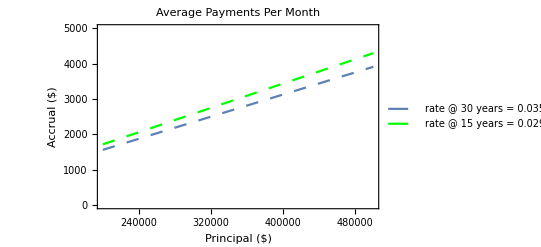

```mathematica
Show[PlotAccrual30perMonth,PlotAccrual15perMonth, PlotRange->{{200000,500000},{0,5000}}]
```

```mathematica
AccrualTable30perMonth
AccrualTable15perMonth
```

(200000 | 1563.86
210000 | 1642.05
220000 | 1720.24
230000 | 1798.43
240000 | 1876.63
250000 | 1954.82
260000 | 2033.01
270000 | 2111.21
280000 | 2189.4
290000 | 2267.59
300000 | 2345.78
310000 | 2423.98
320000 | 2502.17
330000 | 2580.36
340000 | 2658.56
350000 | 2736.75
360000 | 2814.94
370000 | 2893.13
380000 | 2971.33
390000 | 3049.52
400000 | 3127.71
410000 | 3205.9
420000 | 3284.1
430000 | 3362.29
440000 | 3440.48
450000 | 3518.68
460000 | 3596.87
470000 | 3675.06
480000 | 3753.25
490000 | 3831.45
500000 | 3909.64)

(200000 | 1718.51
210000 | 1804.44
220000 | 1890.36
230000 | 1976.29
240000 | 2062.22
250000 | 2148.14
260000 | 2234.07
270000 | 2319.99
280000 | 2405.92
290000 | 2491.84
300000 | 2577.77
310000 | 2663.69
320000 | 2749.62
330000 | 2835.55
340000 | 2921.47
350000 | 3007.4
360000 | 3093.32
370000 | 3179.25
380000 | 3265.17
390000 | 3351.1
400000 | 3437.03
410000 | 3522.95
420000 | 3608.88
430000 | 3694.8
440000 | 3780.73
450000 | 3866.65
460000 | 3952.58
470000 | 4038.5
480000 | 4124.43
490000 | 4210.36
500000 | 4296.28)

## Exponential Interest

```mathematica
rate=0.0351;
n=1;
t=30;
Accrualexp30[Principal_]:=Principal*ⅇ^(rate*t)
Qmax=500000;
Qmin=200000;
Npt=10;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
AccrualexpTable30=Table[{Q[i],Accrualexp30[Q[i]]},{i,0,Npt}]
```

(200000 | 573247.
230000 | 659234.
260000 | 745222.
290000 | 831209.
320000 | 917196.
350000 | 1.00318×10^6
380000 | 1.08917×10^6
410000 | 1.17516×10^6
440000 | 1.26114×10^6
470000 | 1.34713×10^6
500000 | 1.43312×10^6)

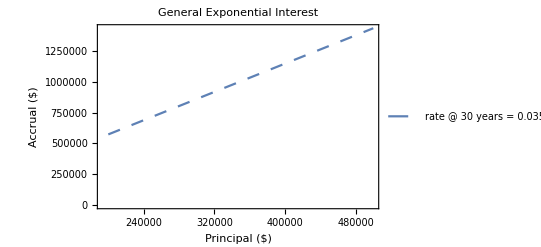

```mathematica
PlotAccrualexp30=ListPlot[%, Joined-> True,PlotStyle->{Dashing[Medium]},PlotLegends->{"rate @ 30 years = 0.0351"},Frame->True,FrameLabel->{"Principal ($)","Accrual ($)"},PlotLabel->HoldForm["General Exponential Interest"],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

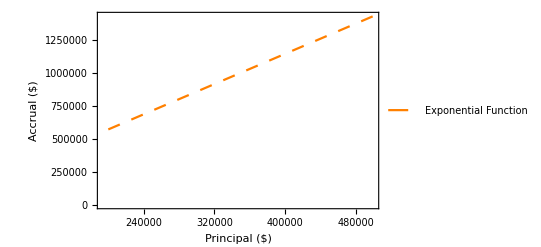

```mathematica
PlotAccrualexp30NT=ListPlot[%%, Joined-> True,PlotStyle->{Dashing[Medium],Orange},PlotLegends->{"Exponential Function"},Frame->True,FrameLabel->{"Principal ($)","Accrual ($)"},LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
rate=0.0295;
n=1;
t=15;
Accrualexp15[Principal_]:=Principal*ⅇ^(rate*t)
Qmax=500000;
Qmin=200000;
Npt=10;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
AccrualexpTable15=Table[{Q[i],Accrualexp15[Q[i]]},{i,0,Npt}]
```

(200000 | 311319.
230000 | 358017.
260000 | 404714.
290000 | 451412.
320000 | 498110.
350000 | 544808.
380000 | 591506.
410000 | 638203.
440000 | 684901.
470000 | 731599.
500000 | 778297.)

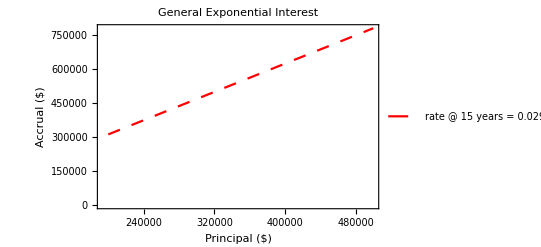

```mathematica
PlotAccrualexp15=ListPlot[%, Joined-> True,PlotStyle->{Dashing[Medium],Red},PlotLegends->{"rate @ 15 years = 0.0295"},Frame->True,FrameLabel->{"Principal ($)","Accrual ($)"},PlotLabel->HoldForm["General Exponential Interest"],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

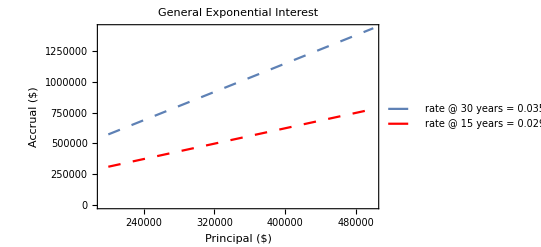

```mathematica
Show[PlotAccrualexp30,PlotAccrualexp15]
```

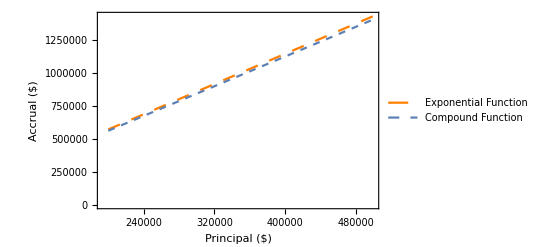

```mathematica
Show[PlotAccrualexp30NT,PlotAccrual30NT]
```

```mathematica
rate=0.00375;
n=1;
t=15;

Testexp15[Principal_]:=Principal*ⅇ^(rate*t)

Qmax=500000;
Qmin=0;
Npt=100;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
TestexpTable15=Table[{Q[i],Testexp15[Q[i]]},{i,0,Npt}];
```

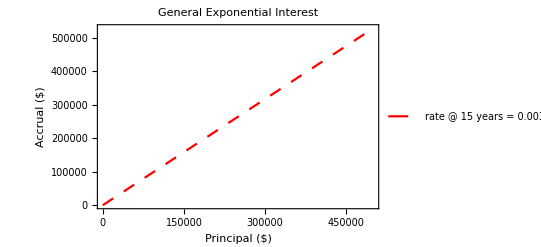

```mathematica
PlotTestexp15=ListPlot[%, Joined-> True,PlotStyle->{Dashing[Medium],Red},PlotLegends->{"rate @ 15 years = 0.00375"},Frame->True,FrameLabel->{"Principal ($)","Accrual ($)"},PlotLabel->HoldForm["General Exponential Interest"],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
rate=0.00375;
n=1;
t=30;
Accrual30perMonth[Principal_]:=Principal(1+rate/n)^(n*t)/(360)
Qmax=500000;
Qmin=200000;
Npt=10;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
AccrualTable30perMonth=Table[{Q[i],Accrual30perMonth[Q[i]]},{i,0,Npt}]
```

(200000 | 621.576
230000 | 714.812
260000 | 808.049
290000 | 901.285
320000 | 994.522
350000 | 1087.76
380000 | 1180.99
410000 | 1274.23
440000 | 1367.47
470000 | 1460.7
500000 | 1553.94)